```mathematica
Par[x_,y_]:=(x y)/(x+y);
Factor[Par[R+ⅈ ω Ls,1/(ⅈ ω Cp)]]
```

-(25000000000000 ⅈ (-100000000000000 ⅈ+3 ω))/(-2500000000000000000000000-100000000000000 ⅈ ω+3 ω^2)

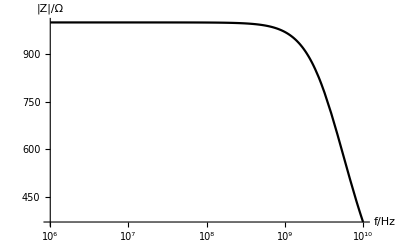

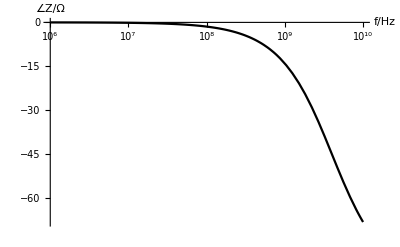

```mathematica
R=1000;Ls=30×10^-12;Cp=40×10^-15;
Z[ω_]:=Par[R+ⅈ ω Ls,1/(ⅈ ω Cp)];
LogLinearPlot[Abs[Z[2 π f]],{f,10^6,10^10},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"f/Hz","|Z|/Ω"}]
LogLinearPlot[Arg[Z[2 π f]]*180/π,{f,10^6,10^10},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"f/Hz","∠Z/Ω"}]
```